```mathematica
int4D[m_] := NIntegrate[ 1/(Sin[Pi p0/2]^2 +Sin[Pi p1/2]^2+Sin[Pi p2/2]^2+Sin[Pi p3/2]^2 +m^2)^2,{p0,-1,1},{p1,-1,1},{p2,-1,1},{p3,-1,1}]
```

```mathematica
int4D[1]
```

2.17852

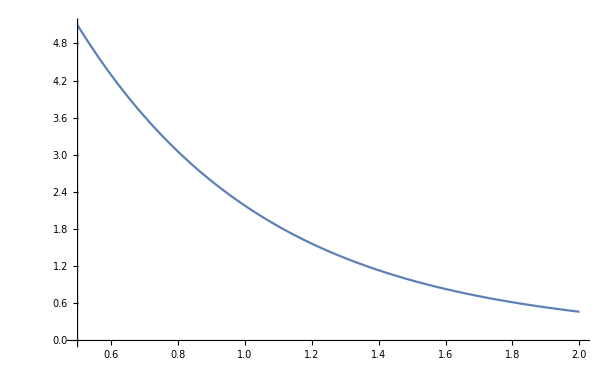

```mathematica
Plot[int4D[m],{m,0.5,2.0}]
```